```mathematica
dir=NotebookDirectory[];
fileName="PK var PEP 5mM ADP.xlsx";
folder="ExampleData";
file=FileNameJoin[{dir,folder,fileName}];
```

```mathematica
repeats=1;
conc=Table[{0,0.1,0.25,0.5,1,2.5,5,10},{i,1,repeats}];
```

```mathematica
proteinDilution=1; (*protein dilution factor before addition to 100μl well*)
proteinConc=3.148/proteinDilution; (*mg·ml^-1 from bradford*)
lysateDilutionInWell=100/20; (*20μl in 100μl assay*)
pathLength=0.26; (*10μl well volume*)
NADHExt=6.22 (*mM^-1 cm^-1*);
```

```mathematica
Table[rangeCheck[i],{i,Length[dataPlots]}]
```

{,,,,,,,}

```mathematica
rangeFileName=StringDelete[fileName,{".xlsx"," "}]<>".mx";
rangeFolder="linearRanges";
```

```mathematica
ranges=Table[range[i],{i,1,Length[dataPlots]}];
(*ranges = Import[FileNameJoin[{dir,folder,rangeFolder,rangeFileName}]]*)
```

```mathematica
rates=-Table[D[fits[[i]][x],x],{i,1,Length[fits]}]*(proteinDilution/(NADHExt*pathLength*proteinConc));
```

```mathematica
(*Export[FileNameJoin[{dir,folder,rangeFolder,rangeFileName}],ranges]*)
```

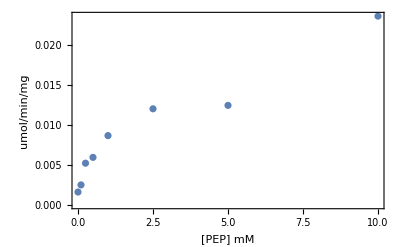

```mathematica
var=ToString@PEP;
ListPlot[Thread[{Flatten[conc],rates}],Axes->False,Frame->True,FrameLabel->{"["<>var<>"] mM","umol/min/mg"},LabelStyle->Directive[Black,FontSize->16],PlotRange->All]
```

```mathematica
rateData=Drop[Thread[{Flatten[conc],rates}]];
headings={{var<>" mM", "V (umol/min/mg)"}};
```

```mathematica
dataForExport=Join[headings,SortBy[rateData,First]];
MatrixForm[dataForExport]
```

(PEP mM | V (umol/min/mg)
0 | 0.00161221
0.1 | 0.00249867
0.25 | 0.00521037
0.5 | 0.00593614
1 | 0.00865146
2.5 | 0.0119987
5 | 0.012424
10 | 0.0224247)

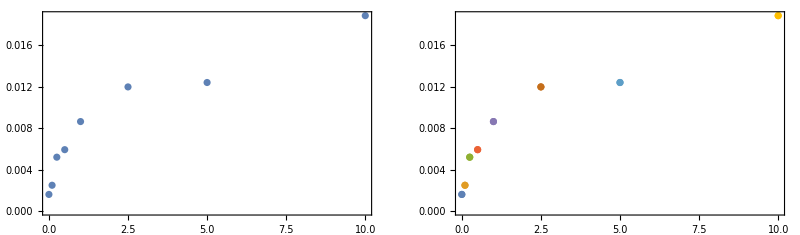

```mathematica
GraphicsRow[{ListPlot[Thread[{DeleteDuplicates@conc[[1]],MeanAround[#[[;;,2]]]&/@GatherBy[rateData,First]}],Axes->False,Frame->True,PlotRange->Full],
ListPlot[GatherBy[rateData,First],Axes->False,Frame->True,PlotRange->All]},ImageSize->Full]
```

```mathematica
(*Export[FileNameJoin[{dir,"data1.csv"}],dataForExport]*)
```

### Data formatting:

```mathematica
allDataHeadings={{"F6P","ATP","ADP","F16BP","AMP","V(umol/min/mg)"}}
```

{{F6P,ATP,ADP,F16BP,AMP,V(umol/min/mg)}}

#### vary F6P

```mathematica
(*dataFormatted={#[[1]],2,0,0,2,#[[2]]}&/@SortBy[rateData,First]*)
```

#### vary ATP:

```mathematica
(*dataFormatted={1,#[[1]],0,0,0,#[[2]]}&/@SortBy[rateData,First]*)
```

#### vary ADP:

```mathematica
(*dataFormatted={10,2,#[[1]],0,0,#[[2]]}&/@rateData*)
```

#### vary F16BP:

```mathematica
(*dataFormatted={2.5,5,#[[1]],0,0,#[[2]]}&/@rateData*)
```

#### vary AMP:

```mathematica
(*dataFormatted={2.5,5,0,#[[1]],#[[2]]}&/@rateData*)
```

#### For Exporting

```mathematica
(*Export[FileNameJoin[{dir,"dataVarF6PwAMP.csv"}],Join[allDataHeadings,dataFormatted]];*)
```